1

Introduction to the Model

## The model

### The Five Assumptions (A.1-A.5, A.2-A.5 are called the Gauss Markov Assumptions)

(A.1): ϵ_tare normally distribute, ϵ ~ N (0,σ^2 I)

(A.2): E(ϵ_t|X_t) = 0

(A.3): Homoskedasticity: Var(ϵ_t|X_t)=σ_t^2 = σ^2, for all t

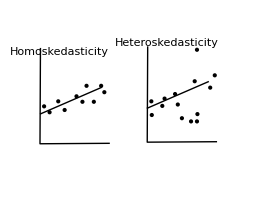

(A.4): No Autocorrelation: Cov(ϵ_t ϵ_s) = 0 t≠s

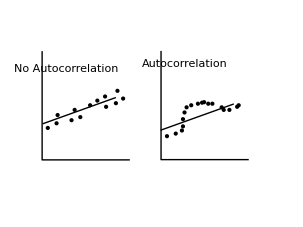

(A.5):  X’s are non-stochastic or in other words the X’s and the ϵ’s are not statistically correlated.

### The Two models (Classical Linear, and Classical Normal Linear)

#### Classical Linear Regression Model (A.2-A.5)

##### Properties

The β̂'s are unbiased: E((β̂)_i) = β_i

The β̂'s are consistent: Var((β̂)_i)-> 0 as n->∞

They have the minimum variable of all linear unbiased estimators (THE ARE BLUE)

OLS≠MLE

They are not normally distributed and therefore t and f stats are not exact.

#### Classical Normal Liner Regression Model (A.1-A.5)

##### Properties

The β̂'s are unbiased: E((β̂)_i) = β_i

The β̂'s are consistent: Var((β̂)_i)-> 0 as n->∞

They have the minimum variable of ALL unbiased estimators (THE ARE BLUE, and more)

OLS=MLE

They ARE  normally distributed and therefore t and f stats are exact.

## Parameter Estimators

We are often presented with a set of (x,y) data pairs and told to estimate a linear relationship between them. In doing this we will have to find a reasonable estimate for a slope constant and also for an intercept constant.

### OLS

#### Derivation

y = Xβ + ϵ = ŷ+ϵ

SSE( β̂) = ∑e_t^2 = ϵ^T ϵ = (y- Xβ)^T(y - Xβ) = y'y-2β̂'X'y+β̂'X'X β̂

(∂SSE)/(∂β̂) = -2X'y+2X' OverHat[Xβ] = 0-> X' OverHat[Xβ] = X'y

β̂ = (X'X)^-1 X'y

#### Properties

minimizes SSE

A.1-A.5 holding determines properties

Normal Equations (∑_(t=1)^n e_t=0 and ∑_(t=1)^n e_t X_t=0. In matrix world it is X'X B̂ = X'y)

OLS ≠ MLE when

OLS ≠  BLUE when

### MLE

#### Derivation

Recall that y ~ N[ Xβ, Σ = Iσ^2]

L(y, μ, Σ) = (e^(-1/2(y-Xβ)^T Σ^-1(y-Xβ)))/((2π)^(n/2)|Σ|^(n/2)) =  (e^(-1/(2 σ^2)(y-Xβ)^T(y-Xβ)))/((2π)^(n/2)|σ^2 I|^(n/2)) = (e^((y-Xβ)^T(y-Xβ)/2 σ^2))/((2π)^(n/2)(σ^2)^(n/2))

l (y,μ,Σ) = ln (L) = ((y-Xβ)^T(y-Xβ))/(2 σ^2)-n/2 ln(2π) - n/2 ln(σ^2) = (-1/σ^2)SSE -n/2 ln(2π) - n/2 ln(σ^2)

(∂l)/(∂β)= 1/(2(σ^Δ)^2)(-2X'y + 2(X'X)β^Δ)=0 (this is the same as above ((∂SSE)/(∂β̂)= 0))

(∂l)/(∂σ^2) = ((y-X β^Δ)^T(y-X β^Δ))/((2(σ^Δ)^2)^2)-n/2)1/((σ^Δ)^2)=0

#### Properties

Maximizes the Log liklihood function

OLS = MLE when assumptions

### BLUE (GLS) estimators β̂ and β^Δ (the Δ is MLE and the ^ is OLS)

There are a few properties these BLUE estimators have to have. They must be linear (β̃ = Ay), they must be unbiased (E(β̃) = AE(y) = AXβ) = β, thus AX= I), they must have minimum variance. Note that method of moments (MOM), MLE ,and OLS all lead to the same β estimator under assumptions A.1-A.5.

#### Derivation (proof) of Expected Value of β̃

E(β̃) = E(Ay) = AE(y) (X'X)^-1 X'E(y) =(X'X)^-1 X' (Xβ) =(X'X)^-1 X'X β = Iβ = β

#### Derivation (proof) of Variance (β)

Var(β)=AΣA' = A(σ^2 I)A'
= (X'X)^-1 X' (σ^2 I) ((X'X)^-1 X')'
= σ^2(X'X)^-1 X'I  X''((X'X)^-1)'
= σ^2(X'X)^-1 X'X''((X'X)^-1)
= (σ^2(X'X))^-1

#### Properties

Consistent Estimators

Minimum variance of linaer unbiased estimators

unbiased

OLS = BLUE iff A.1-A.5 hold.

### Instrumental Variables

## Functional Forms

### Transformable Models

#### Log-Log or Double Log Model

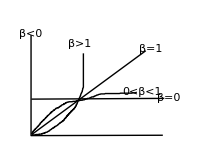

Y_t=AX_t^β ϵ_t
dY/dX=Aβx^(β-1)
η_(Y,X) = dy/dx*x/y = β

You can estimate this with OLS by estimating the model: ln(y) = Ln(a) + βln(x) + ln(ϵt) (reg ly lx)

#### Semi-Log Models

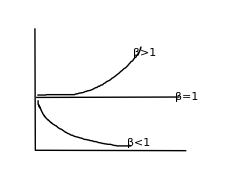

Y_t = Aβ^x_t ϵ_t
dy/dx = Y_t ln(β)
η_(y,x) = X*ln(β)

You can estimate this model by ln(y) = ln(A) + ln(β)*x+ln(ϵ) (reg ly x)

#### Reciprocal Transformations

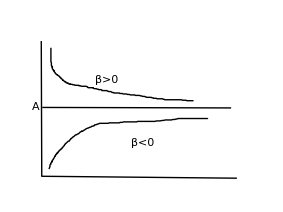

Y_t = A+β/x_t+ϵ_t
dy/dx = -β/x^2
η_(y,x) =-β/(xy)
You can estimate this model by saying Z = 1/x and regressing y = A+βZ+ϵ (reg y z)

#### Logarithmic Reciprocal Transformations

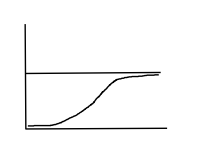

Y_t = e^(A-B/X+ϵ_t)
dy/dx =-βy/x^2
η_(y,x) = β/x

You can estimate this using OLS by saying ln(y) = A- β/x + ϵ then making the substitution Z = 1/x (reg ly Z)

#### Polynomials

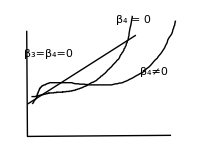

y=  β_1+β_(2x)+β_3 x^2+β_4 x^3

2

Modifications to the Model

## Dummy Variables

Binary Variables: Many variables that you might be interested in don’t have continuous values. Some may have only yes or no (like gender or age above a threshold). If this is the case you have a binary or dummy variable.

Dummy Variables: Other times you have more than just binary responses, but they are still at discrete levels (maybe age, work experience, or education). If this is the case what you will do is set up a dummy variable for each level in your category.

### Models with binary explanatory (independent) variables

An possible model for salary could include a binary variable for whether or not an individual is a college grad. A model for that could be Y_t = α_1+α_2 D_(1t)+ϵ_t where D is the dummy variable. If D = 1 the person graduated from college ,if D=0 they didn’t.

Another model talks about salary and whether or not you are a minority (D_1=1) and whether or not you are female (D_2 =1) Y_t = β_1 D_(1t)+β_2 D_(2t).

In each model you can infer that the coefficient in front of your dummy variable represents the impact on the dependent variable of having the dummy variable be 1.

Dummy Variable Trap: The Dummy Variable Trap is when regressing a model with “n” categories you include “n” slope coefficients. You can avoid the trap by simply leaving out an intercept coefficient or by including n-1 slope coefficients.

Interaction Term:  An interaction term is created by taking the product of two regressors. The Coefficient in front of that joint term is the additive marginal effect of the two regressors (in the case of two dummy variables it is the effect of belonging to both D=1 groups).

If you have things you would like to consider as dummy variables, but they don’t have just two states you will end up creating a binary variable for each level of distinction in that category (for example if you wanted each month would have 12 of them, each corresponding to a particular month).

When you get back coefficient estimates for dummy variables theier interpretation is how much does the dependent variable change if an observation is a yes for that dummy variable. For example if you are looking at salary and one of your dummy variables is female, the coefficient is how much more  (less for (-) value) does a female make than a male.

### Models with binary dependent variables or limited dependent variables

Some good models that you would need binary dependent variables for are testing to see if a student will get in to graduate school, testing to see if someone is likely to Default on a loan, if someone will be married....

#### Linear Probability Model (LPM using OLS)

This model is presented as y_t = α+βx_t+ϵ_t where y=1 if a particular option is taken and 0 if otherwise.

If you do this regression the result will be describing the probability that the first choice was taken.

There are two main problems with this model: A.1 is violated (errors aren’t normal) so is A.5 (correlated error and x’s - heteroskedacity)!! Another problem is that your model is not bounded between 0,1 like it should be for a binary dependent variable.

reg y, X's
predict yhat
gen predy = yhat > .5
tabulate y predy

#### Qualitative Response Models

The idea behind both probit and logit are that they are bounded between 0 and 1 so they make much more sense to use in binary dependent variable case.

(□ | pdf:f(s;θ) | F(z) = ∫_(-∞)^z f(s;θ)
Normal
(Probit) | (e^(-s^2/2))/(√(2π)) | ∫_(-∞)^z (e^(-s^2/2))/(√(2π))
Logistic
(Logit) | e^-s/((1+e^-s)^2) | 1/(1+e^-z)) in all cases Z = Xβ = ŷ.

Marginal Effect of parameters:  The marginal effect of a parameter in a probit or logit model is (∂cdf)/(∂X_it) =β_i*(∂cdf)/(∂β)=  β_i*pdf. This is given to us with the Stata command “ margins, dydx(*) atmeans”

## Lagged Independent Variables (Distributed Lag Models)

Lagged Variable:  A lagged variable is a variable where all of its values are shifted, or lagged,  one period later.

The coefficients in a DLM represent the effect on the dependent variable of the independent variable in teh current period (no lag), from one period before (lagged one period), or from n periods ago (lagged n periods).

You can estimate them using OLS, but there are some problems with that:

How many lags to use (s=?)

the degrees of freedom ( [n-k] = n- 2s -s)

You could have serious multicolinearity issues.

### Alternate Estimation Procedures.

#### Koyck Schemes

The Koyck model assumes that the β_i's decline geometrically, specifically that they follow the formula β_i = β_0 λ^i, 0<λ<1.

With that in mind the Koyck model can be expressed in this way:

Y_t = α (1-λ) + β_0 X_t+λ Y_(t-1)+ ϵ_t-λ ϵ_(t-1)

This can be done in stata by generating a lagged Y (dependent) variable then calling the command reg y x l.y.

#### Polynomial Distributed Lags

This model (PDL) assumes that patterns in teh β_i's can be modeled using general polynomials.

The β’s are defined by this equation:

β_i =α_0+α_1 i+α_2 i^2+....+α_p i^p,

where p is the order of the polynomial. This is repeated for all the lagged β's.

You can test this scheme by comparing LR or chow values for this regression with those from a normal OLS regression.

## Lagged Dependent Variables (Autoregressive Models)

An autoregressive model is an economic modle containing lagged dependent variables.

Below is an example of an autoregressive model:

Y_t = α + βI_t+γY_(t-1)ϵ_t

### Properties of estimators

If ϵ’s uncorrelated with eachother: consistent, biased.  t and F stats are bad

If  ϵ’s are correlated with eachother: inconsistent, biased. t and F stats are bad.

### Interpretation of Coefiicients

Impact Multiplier: In the model above (∂Y_t)/(∂I_t)=β, which is known as the impace multiplier for thi smodel. This measures the change in Y in the same period as I.

Becuase of how the model is defined, we can say that Y_(t-1) = α + βI_(t-1)+γY_(t-2) and  Y_(t-2) = α + βI_(t-2)+γY_(t-3) and so on. We can then re-write Y_t = α (1+γ+γ^2+...) + β (I + γ I_(t-1)+ γ^2 I_(t-2)+...) = α/(1-γ)+βI_t+βγI_(t-1)+βγ^2 I_(t-2)+.....

Total Impact (Long Run Investment Multiplier): From the above equation we can say that the impact a change in I has on Y is defined as β/(1-γ). This is interpreted as the cumulitive (over time) change in Y corresponding to a one time change  in I or the increase in long-run equlibirum Y corresponding to a sustained increase in I.

### Tests for Autoregressive Models

You will often have problems with autocorrelation if you use an AR model so to test if this is teh case you can use the Durbin h or Breuch Godfrey tests.

#### Durbin h test

The test is defined as follows:

h = ρ (n/(1 - nVar(Coef. est. of Y_(t-1))))^(1/2)

This test has an asymptotic distribution of h ~ N (0,1).

There are two main problems with this test:

The h test is invalid if n Var (cof. est. Y_(t-1)) >1

N(0,1) seems to give a poor fit ot teh distributio of h for frequently encountered sample sizes.

#### Breuch-Godfrey Test

This test can be preformed by regresion the OLS e_t's on the lagged y’s and lagged e_t's and then testing the collective explanatory power of the coefficients of the lagged errors using an F-test.

## Simultaneous Equations

3

Violations of the 5 Assumptions

## A.1: Errors are not normally distributed

### Causes

This isn’t really a cause, but sometimes the distribution of error temrs is too tall and pointed. This usually means they follow a Laplace distribution, or that they are LAD. This isn’t desireable, but it is something we know how to work with. To obtain LAD estimators for β’s we use the qreg command.

### Tests

#### Skewness

A normal distribution is symmetric about the mean. This means is a property known as skewness and the expected value for the skewness in a perfectly symmetric distribution is 0. We can create parameter estimates for the skewness in this way (after creating the estimate we can use a normal t test with H_0: skewness =0):

(γ̂)_1 = (∑_(t=1)^n ϵ_t^3/n)/((∑_(t=1)^n ϵ_t^2/n)^(3/2))~N (0, 6/n)

#### Kurtosis

The other part of a normal distribution is known as the kurtosis of the distribution. With a perfect standard normal distribution the kurtosis is equal to 3. A similar test statistic can be computed in the following way:

(γ̂)_2 = (∑_(t=1)^n ϵ_t^4/n)/((∑_(t=1)^n ϵ_t^2/n)^2)-3~N(0,24/n)

The (-3) in the test is accounting for the fact that the expected value is 3 and allows this statistic to return just the excess kurtosis.

#### JB Test

The JB test is kinda a summary of the two to get a picture of the overall normality of the distribution of the error terms.  It is defined as follows:

JB = n [ skewness^2/6+ (excess kurtosis)^2/24] ~ χ^2(2)

### Consequences

OLS = BLUE, but may not be efficient.

OLS ≠ MLE

t and F stats are not exact.

Unibiased, but non-linear estimators mught have lower variance.

### Fixes

You can obtain  LAD estimates by using the STATA command qreg When you do this you are assuming that the variance is bigger. This is often done if tehre are a fiarly large number of outliers in your data.

You could also consider using other estimators with different distributions.

The last idea is to just delete some of the outliers in your data to try to get the distribution to behave a little better.

## A.2 Expected Value of error terms is not 0

### Causes

### Tests

### Consequences

If A.2 doesn’t hold then all of the least squares estimators in the vector β̂ will be biased. There is a change that if the expected value of the error terms are all equal to μ, then you can show that only the slope term is biased.

### Fixes

## A.3 Variance of errors are not homoskedastic

### Information

The definition of heteroskedasticity in the error terms is that the error term for each observation is not equal.

### Causes

This is common with cross-sectional data.

### Tests

The main idea behind the different tests is that that you try to find some kind of systematic behavior in the variances of the errors.

#### Goldfield Quandt Test

H_0: σ_1^2 = σ_2^2=...=σ_n^2 (homoskedasticity)

You then divide the data in three groups (about the same size).

Then run separate regressions on groups I and III and s_I^2 and s_III^2 are estimators for σ^2

There is then a test statistic s_III^2/S_I^2~F (n_3-k, n_1-k).

We would expect the stat to be close to 1 (variance of error terms are similar). The further away we are the more reason to reject H_0

#### Modified White Test

### Consequences

Estimators are still unbiased.

They are still consistent.

They are NOT minimum variance.

They are NOT BLUE.

The t and F stats aren’t exact [this is because the wrong formula is used in computing them].

### Fixes

To fix the mistake with the bad t and F stats we simply need to use the write equaitons when calculating the standard errors. This can be done using the STATA command reg y s’s, robust (The equation that was used is (s^2(X'X))^-1 when it should have been (X'X)^-1 X'ΣX (X'X)^-1)

YTou can also use the command vwls y x’s, sd (std. error)

## A.4 Autocorrelation in the error terms

When you have autocorrellation the error terms are not statistically independent.

### Causes

This is very common in time-series data.

### Tests

Before dong any kind of autocorrelation test you will need to specify a time variable using the STATA Command tsset t (where t is that time variable. This is easily created with the command gen t = _n

#### Durbin-Watson

The test will be testing the hypothesis that there is no autocorrelation. (H_0: no autocorrelation)

The DW test stat is defined as follows:

DW = (∑_(t=2)^n (e_t-e_(t-1))^2)/(∑_(t=1)^n e_t)≈ 2(1-ρ), (ρ is the corr between e_t and e_(t-1))

We want this statistic be as close to 2 as possible. The closer to 2 we are the less autocorrelation there is in our data.

In this test you will have two clear regection regions on the outsides (this is bad), a clear fail to reject region in the middle, and ambiguous regions in between.

#### Woolridge test

This one is simple. You will do a regression of the error term with the error term from one period ago.

You hope that there is not a statistically significant relationship between the 2 (shown by t stat and p-value reported with regression) so you can reject the idea of autocorrelation.

#### Other things for Autoregressive models

##### Durbin-h test

The test stat is defined as follows

h = (1-DW/2)√(n/(1-(ns^2)_(lagged _y coefficient)))~N[0,1]

##### Breuch Godfrey Test

This is similar to the woolridge, but you will be regressing the error terms on lagged y’s and lagged e’s.

You will use the F-stat produced by the regression to see if there is any explanatory power in that. If there is you have autocorrelation.

### Consequences

They are still unbiased.

They are still consistent

THey are NOT minimum variance. (can be fixed by using the equation (X' Σ^-1 X)^-1 X' Σ^-1 Y and then OLS = MLE = GLS)

They are NOT BLUE

The t and F stats are not valid. (fix using (X'X)^-1 X' Σ^-1(X(X'X))^-1

### Fixes

#### Transforming the model

You can change the model using various transformation matricies T that have the characteristic that TX = I and that T’T = Σ.

There are two matricies you could use: T_1 = (-ρ | 0 | ... | 0
0 | -ρ | ... | 0
... | ... | ... | ...
0 | 0 | 0 | -ρ) or T_2 = (√(1-ρ^2) | 0 | ... | 0
T_1 |  |  | 
 |  |  | 
 |  |  | )

You can do this in STATA using the commands prais y x’s, corc (for T_1) and prais y x’s (for T_2)

The difference between T_1 and T_2 is that you use one less observation than you have if you use T_1, but T_2 doesn’t drop one.

#### Newey

If you use the command newey y x’s, lag(.75 n^(1/3)) you will correct the t and F stats, but not get rid of the Autocorrelation. It is like using the robust command in the case of heteroskedasticity in that is just makes STATA use the correct formula for the standard errors.

## A.5 Non-stoichastic X’s

Of all the assumptions that could be viotlated, a violoation of A.5 has the most severe consequences.

This is the result when the independent variables are correlated with the error terms.

This is common when you have endogeneous regressors.

### Causes

Endogenous regressors

### Tests

#### Hausman test

You will have to do a normal OLS regression then tell it the command est store OLS.

Then do ivregress 2sls y (x’s=instruments)  and then est store iv

Then the last test is you need to say hausman iv ols

The purpose of this is to do a regression using OLS and then do one using a two-step process for adding the instrumental variables and then comparing the two to see if there is a significant difference.

### Consequences

They are biased.

They ARE inconsistent

They are NOT BLUE

They are NOT minimum variance.

### Fixes

4

Extra Material

## Definitions

Adjusted R^2 :(R^-)^2 = 1 (SSE/(n-k))/(SST/ (n-1)).  The great thing about this is that with the addition new independent variables, the adjusted r-squared will only increase in value if the t-statistic associated with the new variable is greater than 1 in absolute value (it is significant)

Asomptotic Distribution:  f(θ̂) is the asmptotic distribution of θ̂ if the exact distribution of θ̂ approaches f(θ̂) as the sample size increases. The actual distribution can be equal to the asymptotic distribution, but doesn’t have to be. This is pretty much like the central limit theorem saying that as n gets bigger the distribution converges to what it should be.

Autocorrelation: Autocorrelation often exists in time-series data if the error terms in different time periods are correlated. This makes OLS ≠ BLUE.

Auto-regressive models: An auto-regresive model is one that has lagged dependent variables.

ANOVA: ANOVA stands for analysis of variance and is usually represented in a table in this way:

Source of Variation | SS_ | d.f. | MSE
Model
Error | SSR
SSE | K-1
n-K | SSR/(K-1)
SSE/(n-K)
Total | SST | n-1 | SST/n-1

Binary or Dummy Variable: Variables that can only have values of 0 or 1 can be used to model qualitative characteristics (gender, race...). If you have a qualitative characteristic is associated with k categories, you can only include k-1 binary variables or you could include k variables and no intercept term. If you include k binary variables and an intercept you fall into the dummy variable trap.

Confidence Intervals: A rule is used to construct a random interval so that a certain percentage of all data sets, determined by the confidence level, yields an interval that contains the population value. Essentially when you are estimating the value of something you can’t get it perfect. A confidence interval is a range of values which we can say we are x % confident that the true value lies in the range.

Consistent Estimator:p lim_(n → ∞) (θ̂) = θ , or bias(θ̂) →0 and the var (θ̂) → 0  as n→ ∞.

Cross Sectional-Data: This is a data set corresponding to a single point in time.

Distributed Lag Models: A time series regression model which includes lagged values of the explanatory variable. Koyck and polynomial distributive lag (PDL) specifiactions are used to help with multicolinearity.

Dummy Variable Trap: This happens when you have a binary variable with k categories and you include k binary variables and an intercept term in a regression.

Efficient Estimator: An estimator is said to be efficient when it is the minimum variance unbiased estimator. If A.1-!.5 hold, then OLS is BLUE and efficient. If A.1 doesn’t hold OLS is still BLUE, but no efficient because there may be a better unibased (nonlinear) estimator with a smaller variance.

Endogenous Regressor: An endogenous regressor is an “explanatory” variable that is correlated with the model’s error term. This means there is feedback between the dependent variable and the independent variable in question (we always takled about salary and education). When there are endogenous regressors the OLS estimators are biased and inconsistent.

F-test: A test stat that can be used to test hypothesis with multiple constraints on the parameter estimates. There is an F stat that is normally reported with a regresion that tests the null hypothesis that all slope coefficients are equal to zero. This is constructed as follows: F = ((R^2/(k-1))/((1-R^2)/ (n-k)))~F(k-1,n-k)

Elasticities associated with different functional forms: Elasticity  = (%Δy)/(%Δx) = dy/dx x/y. Finding percentage changes is done easily in a regression analysis by taking the natural log of a variable. For example if you had log(salary) = stuff + log(hours) the elasticiy of horus on salary is going to be the coefficient in front of log(hours). This is because the log makes it a percentage change in...

Gauss Markov Assumptions: These are A.2-A.5. The normality in the error terms (A.1) is not included. This leads to the general linear regression model.

Hedonic Pricing Model: A hedonic pricing model expresses the price of a good in terms of its attributes. They are very common in real estate when you do a regression to determine the effect of a bedroom, bathroom, lot size, or square footage on the price of the home.

Heteroskedasticity: This is when the error terms do not all have the same value. This is a violation of A.3 and makes OLS ≠BLUE.

Instrumental Variables: If you have endogenous regressors in your model, an instrumental variable can be used in its place. The instrumental variable will need to NOT be correleted with the dependent variable (that was the problem with the endogenous one), but it must be correlated to the endogenous regressor. This will allow the model to have the same explanatory characteristics, but avoid the biased and inconsistent problems.

Instrumental Variables Estimators:

Interaction Terms: A regressor in a model which involves the product of two explanatory variables. It results in the marginal impact of one independent variable on the dependent variable as it depends on another independent one.

Koyck Distributive Lag Models: A time series regression model that includes lagged values of the independent variables. This model assumes that the β’s associated with an explanatory variable deline geometrically (see above for more information).

Kurtosis: The kurtosis is a rough estimate of the pointiness of a distribution as well as the thickness of the tails. The kurtosis for the normal distribution is 3.

Liklihood Ratio Test: A liklihood ratio test (LR test) can be used to investigate the valitidy of a joint hypothesis of coefficietns. It is constructed by estimating the constrained model, the unconstrained model and getting log liklihood values for both. The test statistic is then constructed in this way: LR = 2  (l-l*)~χ^2(r)

Linear Probability Model: This is just a model that has the dependent variable as a binary variable. These have problems of the errors not being normally distributed (A.1 violated), there will be heteroskedasticity (A.3 is violated), and you could get values outside the range [0,1] which just doesn’t make sense.

Logit Model: This is a different model that helps with binary dependent variables (doesn’t have the 3 problems listed above). The cool thing is that it the values are bounded between 0 and 1.  It is defined as Pr (Y=1|x) = ∫_(-∞)^(X_t β) f(s)ⅆs = F(X_t β) where f(s) is the log-logistic pdf. The marginal effect are given by (∂Pr (Y=1|x))/(∂X_i) = β_i f(X_t β) (STATA only gives you β_i normally).

Multicolinearity: Multicolinearity reers to non-zero correlations between the explanatory variables in a regression model. Increased multicolinearity reduces accuracy of parameter estimates. If you see a large F stat and small t stats you usually have multicolinearity.

Normal Equations: The normal equations are the necessary conditions associated with minimizing hte SSE in a linear ergression model. X’Xβ = X’Y and can also be written as X’e =0 where e represents the estimated arrors. X’e=0 implies that teh y’s and e’s are orthogonal.

Panel Data: Panel data is a data set made from cross-sections over time. This means it is both time-series and cross-sectional. The panel is said to be balanced if there is the same number of observations for each point in time.

Polynomial Distributive Lag (PDL) models: When you have time-series data and want to include lagged independent variables you can model their collective effect using a polynomial. This specification can be tested (to see if it is a good idea) by doing a Chow or LR test on the mdoel including the PDL and the normal OLS model before that.

Probit Model: This is a the same as the logit model with one difference (the function f(s)). The cool thing is that it the values are bounded between 0 and 1.  It is defined as Pr (Y=1|x) = ∫_(-∞)^(X_t β) f(s)ⅆs = F(X_t β) where f(s) is the standard normal pdf. The marginal effect are given by (∂Pr (Y=1|x))/(∂X_i) = β_i f(X_t β) (STATA only gives you β_i normally).

P-value: When you preform a hypothesis test there will be a certain probability associated with the chances of being greater than the test-statistic (according to a certain distribution).

Qualitative Response Model: A model for binary dependent variables, where the predictied probabilities are constrained from (0,1). The Logit and Probit models are example. More genearally, you can construct a QRM using any valid pdf as the function f(s).  See the distributions and marginal effects described under Logit Model or Probit Model

R^2 (coefficient of determination): R^2 = SSR/SST = 1 - SSE/SST. The coefficient of determination for an OLS regression is a value between 0 and 1 that gives a general idea of the “goodness of fit” in the model.

Reduced Form: The reduced form representation of a structural model expresses each dependent variable in terms of explanatory variables endogenous, current exogenous, and lagged exogenous variables).

Skewness: Definition: E (Y-μ)^3/σ^3. The skewness is a measure of symmetry (if it equals 0 it is perfectly symetric). Positive skewness is associated with a long thick tail to the right . If the skewness is negative the long thick tail will be on the left.

Structural Representation of an Econometric Model: This is a mathematical representatio of the relationship between economic variables imlied by economic theory and may include endovenoug regressors along with exogenous variables on the right hand side of the equations.

Time-Series Data:  Data collected regularly over a period of time.

Unbiased Estimator: θ̂ is an unbiased estimator of θ if E (θ̂)= θ.

Useful Theorem:  If y~N[μ_y,Σ_y] then Z = Ay~N[μ_z = Aμ_y, Σ_Z = AΣ_y A^T] where A is a matrix of constant. Proof:

E(z) = E(Ay) = A E(y) = Aμ_y
Var (Z) = E((z-E(z))(z - E(z))
= E[(Ay - Aμ_y) (Ay -Aμ_y)^T]
= A E[(y - μ_y)(y- μ_y)]A^T
= A Σ_y A^T

Variance of the Prediction (or of the forecast error):

-Graphics-

## Statistical Inference

### Basic Properties

Biased/Unbiaed: An estimator is unbiased if its expected value is equal to the true value.

Consistent: an estimator is consistent if its bias and varize approach zero as the sample size increases.

Efficient/Minimum Variance

BLUE (best linear unbiased estimator)

### Tests

#### T Tests

A t-test is used when you want to check hypothesis about a single parameter or a linear combination of parameters (sometimes useful when you have a Cobb-Douglas production function and you want ot check for constant returns to scale, for example).

There is always a null hypothesis (H_0) associated with a t-statistic. STATA will report the t-statistic and a p-value. That p-value is the probability of getting a t-stat greater than the one you did. If you are testing at an α = 5% level and this p-value is greater than 0.05 you are not in the rejection region and you cannot reject H_0. If the p-value is less than 0.05 you are in the rejection region and H_0 will be rejected.

To preform a t-test in STATA type the command test.

#### F-tests

An F-test is used when you want to test a hypothesis that puts multiple constraints on parameters.

The standard F-test reported with any STATA regression is the test for H_0: all slope coefficients =0. There will be a F-value and a p-value given. You usually want to reject this hypothesis so you are going for a p-value < 0.05.

This can also be done using the STATA command test. But instead of giving a single parameter or a linear combination of parameters you give more than one equal sign in the command. (this means you are imposing more than one constraint one the parameters).

##### Chow Test

In this case we will look at the R^2values and compare them in a ratio using an F statistic. Note that R, SSE without a * are before the restrictions and if they have a * are after the restrictions.

F= ((SSE*-SSE)/r)/((SSE)/(n-k))= (R^2-R^(2*))/(1-R^2)(n-k)/r~F(r,(n-k)) where r = # of restrictions imposed on model.

#### LR Tests

The theory or idea behind this is about he same, but instead of focusing on the R^2 or SSE it focuses on the log likelihood value l.

If your hypothesis wasn't very good you should see a rather large drop in l. On the other hand if your hypothesis is really good you should see very little change.

LR = 2 (l-l*)  = (SSE^*- SSE)/σ^2 = n ln(1/(1-R^2)) = -nln(1-R^2)~ χ^2(r), again r is the number of restrictions.